## Willy Martin MATH 4503 Homework #5 I received assistance from Cameron Alred Modified Section 5.4, Problem #27, done using Euler’s method and Mathematica

Sec. 5.4  Problem 27. The irreversible chemical reaction in which two molecules of solid potassium dichromate (K_2 Cr_2 O_7), two molecules of water (H_2 O), and three atoms of solid sulfur (S) combine to yield three molecules of the gas sulfur dioxide (SO_2), four molecules of solid potassium hydroxide (KOH), and two molecules of solid chromic oxide (Cr_2 O_3) can be represented symbolically by the stoichiometric equation:
2 K_2 Cr_2 O_7+2 H_2O+3 S⟶4 KOH+2 Cr_2 O_3+3SO_2.
If n_1 molecules of K_2 Cr_2 O_7,n_2 molecules ofH_2 O,and n_3 moleculesSare originally available,the following differential equation describes the amountx(t)ofKOHafter timet,wheretis measured in seconds:

   (d x)/(d t)=k (n_1-x/2)^2 (n_2-x/2)^2(n_3-(3x)/4)^3,where k is the velocity constant of the reaction. Ifk=6.22×10^-19,n_1=n_2=2×10^3,andn_3=3×10^3,how many units of potassium hydroxide will have been formed after 0.2 seconds?

```mathematica
Remove[ "Global`*"]
```

```mathematica
constants = {k-> 6.22*10^-19,Subscript[n, 1]-> 2000, Subscript[n, 2]-> 2000, Subscript[n, 3]-> 3000};
```

```mathematica
Subscript[t, 0]=0;Subscript[x, 0]=0;Subscript[t, f]=0.2;
```

```mathematica
f[t_,x_]:=k*(Subscript[n, 1]-x/2)^2 (Subscript[n, 2]-x/2)^2(Subscript[n, 3]-(3x)/4)^3/.constants
```

```mathematica
ode=x'[t]==f[t,x[t]]
```

x'[t]==6.22×10^-19 (3000-(3 x[t])/4)^3 (2000-x[t]/2)^4

```mathematica
ic=x[Subscript[t, 0]]==Subscript[x, 0]
```

x[0]==0

Setting the initial conditions of the differential equation.

```mathematica
sol=NDSolve[{ode,ic},x[t],{t,Subscript[t, 0],Subscript[t, f]}]//Flatten
```

{x[t]→InterpolatingFunction[…][t]}

```mathematica
exact[t_]=x[t]/.sol
```

InterpolatingFunction[…][t]

Constructing the analytical solution for the given differential equation.

```mathematica
Print["The differential equation is x'(t)= ",  f[t,x[t]], "with an initial condition x(t_0)= ",Subscript[x, 0]]
```

The differential equation is x'(t)= 6.22×10^-19 (3000-(3 x[t])/4)^3 (2000-x[t]/2)^4with an initial condition x(t_0)= 0

```mathematica
h=0.005
```

0.005

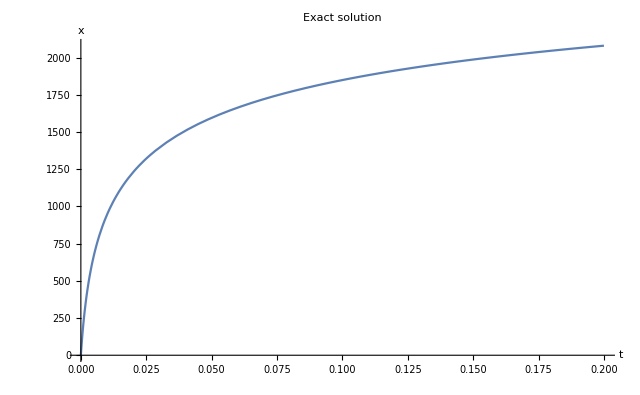

```mathematica
plot1=Plot[exact[t],{t,Subscript[t, 0],Subscript[t, f]},PlotLabel->"Exact solution", AxesOrigin->{-0,0},AxesLabel->{"t","x"}]
```

```mathematica
eulersMethod[f_,t0_,α_,tf_,h_,y_]:=Module[{},
t[0]=t0;
w[0]=α;
n=Rationalize[(tf-t0)/h];
Print["Initialization:\ni=",0,"     t_0=",t[0],"     w_0=",w[0],"     y(t_0)=",y[t[0]]];
Do[
w[i]=w[i-1]+h*f[t[i-1],w[i-1]];
t[i]=t[i-1]+h ,
{i,1,n}];
Print["             Euler's Method and Exact Results"];
TableForm[Table[{i,t[i],w[i],y[t[i]],Abs[w[i]-y[t[i]]]}, {i,0,n,5}],TableHeadings->{None,{"i","t_i","Euler's \nMethod \nw_i","Exact \nSolution\nx(t_i)","Absolute \nError \n|w_i-x(t_i)|\n"}},TableAlignments->Center,TableSpacing->{2,5}]]
```

```mathematica
eulersMethod[f,Subscript[t, 0],Subscript[x, 0],Subscript[t, f],h,exact]/.constants
```

Initialization:
i=0     t_0=0     w_0=0     y(t_0)=0.

Euler's Method and Exact Results

i | t_i | Euler's 
Method 
w_i | Exact 
Solution
x(t_i) | Absolute 
Error 
|w_i-x(t_i)|

0 | 0 | 0 | 0. | 0.
5 | 0.025 | 1580.36 | 1320.87 | 259.492
10 | 0.05 | 1743.09 | 1594.72 | 148.366
15 | 0.075 | 1849.56 | 1745.93 | 103.621
20 | 0.1 | 1927.98 | 1848.58 | 79.4042
25 | 0.125 | 1989.68 | 1925.45 | 64.2315
30 | 0.15 | 2040.29 | 1986.45 | 53.8423
35 | 0.175 | 2083.05 | 2036.76 | 46.2887
40 | 0.2 | 2119.96 | 2079.41 | 40.5534

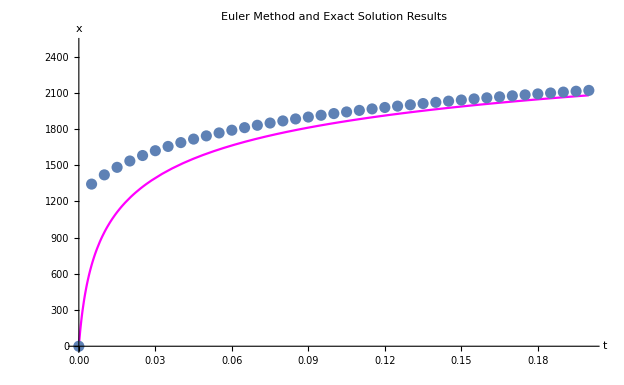

```mathematica
Show[Plot[exact[t],{t,0,0.2},PlotStyle->Magenta,PlotLabel-> "Euler Method and Exact Solution Results",AxesLabel->{"t","x"},PlotRange->{{0,0.2},{0,2500}}],
ListPlot[Table[{t[i],w[i]},{i,0,n}]]]
```

As Euler’s method began to run as shown above, it contained a very large error that reduced as the iterations increased. The final error value was still significantly larger than what is considered to be an acceptable value.

```mathematica
eulersMethod[f,Subscript[t, 0],Subscript[x, 0],Subscript[t, f],0.001,exact]/.constants
```

Initialization:
i=0     t_0=0     w_0=0     y(t_0)=0.

Euler's Method and Exact Results

i | t_i | Euler's 
Method 
w_i | Exact 
Solution
x(t_i) | Absolute 
Error 
|w_i-x(t_i)|

0 | 0 | 0 | 0. | 0.
5 | 0.005 | 726.613 | 672.086 | 54.5264
10 | 0.01 | 986.166 | 944.207 | 41.9595
15 | 0.015 | 1144.72 | 1111.06 | 33.654
20 | 0.02 | 1257.76 | 1229.68 | 28.0821
25 | 0.025 | 1344.98 | 1320.87 | 24.1127
30 | 0.03 | 1415.63 | 1394.48 | 21.1437
35 | 0.035 | 1474.76 | 1455.92 | 18.8381
40 | 0.04 | 1525.46 | 1508.47 | 16.9948
45 | 0.045 | 1569.73 | 1554.25 | 15.4863
50 | 0.05 | 1608.95 | 1594.72 | 14.2283
55 | 0.055 | 1644.09 | 1630.93 | 13.1627
60 | 0.06 | 1675.88 | 1663.63 | 12.2481
65 | 0.065 | 1704.87 | 1693.42 | 11.4543
70 | 0.07 | 1731.49 | 1720.73 | 10.7585
75 | 0.075 | 1756.08 | 1745.93 | 10.1436
80 | 0.08 | 1778.9 | 1769.31 | 9.59604
85 | 0.085 | 1800.18 | 1791.08 | 9.10534
90 | 0.09 | 1820.11 | 1811.45 | 8.66295
95 | 0.095 | 1838.83 | 1830.57 | 8.26199
100 | 0.1 | 1856.48 | 1848.58 | 7.8969
105 | 0.105 | 1873.16 | 1865.59 | 7.56302
110 | 0.11 | 1888.96 | 1881.71 | 7.25649
115 | 0.115 | 1903.98 | 1897.01 | 6.97404
120 | 0.12 | 1918.28 | 1911.57 | 6.71292
125 | 0.125 | 1931.92 | 1925.45 | 6.4708
130 | 0.13 | 1944.95 | 1938.71 | 6.24566
135 | 0.135 | 1957.43 | 1951.39 | 6.03577
140 | 0.14 | 1969.39 | 1963.55 | 5.83962
145 | 0.145 | 1980.88 | 1975.23 | 5.65588
150 | 0.15 | 1991.93 | 1986.45 | 5.48341
155 | 0.155 | 2002.57 | 1997.25 | 5.32119
160 | 0.16 | 2012.82 | 2007.65 | 5.1683
165 | 0.165 | 2022.71 | 2017.69 | 5.02406
170 | 0.17 | 2032.27 | 2027.39 | 4.88762
175 | 0.175 | 2041.52 | 2036.76 | 4.75845
180 | 0.18 | 2050.46 | 2045.83 | 4.63596
185 | 0.185 | 2059.13 | 2054.61 | 4.5196
190 | 0.19 | 2067.54 | 2063.13 | 4.40899
195 | 0.195 | 2075.69 | 2071.39 | 4.30366
200 | 0.2 | 2083.61 | 2079.41 | 4.20325

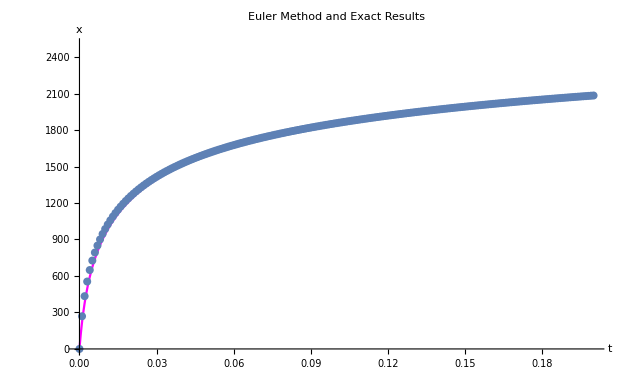

```mathematica
Show[Plot[exact[t],{t,0,0.2},PlotStyle->Magenta,PlotLabel-> "Euler Method and Exact Results",AxesLabel->{"t","x"},PlotRange->{{0,0.2},{0,2500}}],
ListPlot[Table[{t[i],w[i]},{i,0,n}]]]
```

Changing the value of h from 0.005 to 0.001 will cause the plot as shown above to have a more accurate result on the initial derivative. It will also cause a longer run time and more iterations. The iterations above are shown for every fifth interion since it will cause a large table. The solution was also much more accurate as the error term was significantly smaller with a value of 4.20325compared to 40.5534. The error term after 200 iterations was still relatively large compared to other numerical methods, rendering Euler's method impractical for solving many ODE's. Depending on what method is used to solve the given differential equation, the output is 2083 units for Euler's method and 2079 for an exact method.